```mathematica
SetDirectory["/home/czhou/Projects/InvEHL/resources"];
```

```mathematica
Dimensions@xy
```

{16800,2}

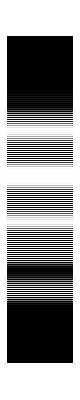

```mathematica
ArrayPlot@Import["./abc.txt","Table"]
```

```mathematica
?ViewProjection
```

```mathematica
c=Flatten[Import["./control.txt","Table"],1];
xy=Import["./mesh/node.txt","Table"];
xyc=Table[{xy⟦i,1⟧,xy⟦i,2⟧,1+c⟦i⟧},{i,1,Length@c}];
Dimensions@xyc
```

{12288,3}

```mathematica
64*48*4
```

12288

```mathematica
h=Flatten[Import["./state/200.txt","Table"],1];
xyh=Table[{xy⟦i,1⟧,xy⟦i,2⟧,h⟦i⟧},{i,1,Length@h}];
Show[ListPlot3D[{xyh,xyc},BoxRatios->{Automatic,Automatic,6},
InterpolationOrder->1,
PlotRange->{{Max@xy⟦All,1⟧,Min@xy⟦All,1⟧},{Max@xy⟦All,2⟧,Min@xy⟦All,2⟧},{0,1.2}}],Plot3D[0,{x,0,19},{y,0,19}],
Boxed->False,
ViewProjection->"Orthographic",ViewPoint->5{1,1,1},
ImagePadding->0,PlotRangePadding->0,Method->{"ShrinkWrap"->True}]
```

-Graphics3D-

```mathematica
"
```

```mathematica
(*
Import["./cat.jpg"];
ImageTake[%,20{1,-1},{1,-1}]
ImagePad[%,{{-10,-10},{-1-10,-1+10}},1]
Export["cat.jpg",%]*)
```

-Graphics-

```mathematica
-Graphics-//std::cout <<b.size();
```

cat.jpg

```mathematica
o0=ListContourPlot[(ImageData@ImageResize[Import["images/heart.png"],{200,200}])⟦All,All,1⟧,ImageSize->500,PlotRange->All,Contours->10,PerformanceGoal->"Quality"]
```

-Graphics-

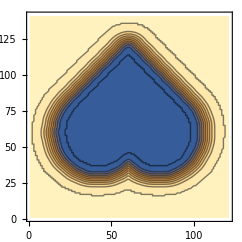

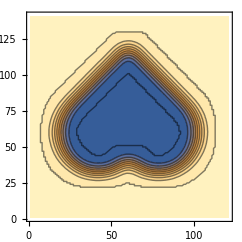

```mathematica
min=0.000;
max=1;
imgSize=2*121;
ct=Range[min,max,(max-min)/10];
img=Import["output_ls.png"];Dimensions@ImageData@img;
o1=ListContourPlot[(ImageData@Import["output_ls.png"])⟦All,All⟧,ImageSize->imgSize,PlotRange->All,Contours->ct,PerformanceGoal->"Quality"]
img=Import["output_gf.png"];Dimensions@ImageData@img;
o2=ListContourPlot[(ImageData@img)⟦All,All⟧,ImageSize->imgSize,PlotRange->All,Contours->ct,PerformanceGoal->"Quality"]
```

```mathematica
ListPlot3D[ImageData@Import["output_gf.png"],BoxRatios->{1, 1, 0.2},
PerformanceGoal->"Quality",ImageSize->1000,PlotRange->All]
```

-Graphics3D-